### 1D analytic qho

```mathematica
Clear["Global`*"]
ℏ=1.;
ω=1.;
m=1.;

npoints=500;
xmin=-20.;
xmax=20.;
x=Subdivide[xmin,xmax,npoints-1];

α=Sqrt[m*ω/ℏ];
f[x_,n_]:=Sqrt[1/2^n/n!]*(m*ω/Pi/ℏ)^0.25*Exp[-α^2*x^2/2.]*HermiteH[n,α*x];
isOrthonormal[x_,n1_,n2_]:=Integrate[f[x,n1]*f[x,n2],{x,-Infinity,Infinity}];
```

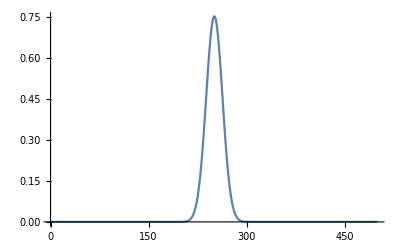

```mathematica
ListPlot[f[x,0],PlotRange->All,Joined->True]
```

```mathematica
Clear[x];
isOrthonormal[x,2,3]
```

0.

### 1D numeric qho

```mathematica
(* see also https://physics.stackexchange.com/questions/766875/numeric-solution-vs-analytic-solution-1d-quantum-harmonic-oscillator *)
Clear["Global`*"]
ℏ=1.;
m=1.;
ω=1.;
npoints=500;

xmin=-20.;
xmax=20.;

x=DiagonalMatrix[Subdivide[xmin,xmax,npoints-1]];
dx=x[[2,2]]-x[[1,1]];
potential=m*ω^2/2.*(x.x);

kinetic=-ℏ^2/2./m*(DiagonalMatrix[Table[-2,npoints]]+DiagonalMatrix[Table[1,npoints-1],1]+DiagonalMatrix[Table[1,npoints-1],-1])/dx^2;

hamiltonian=kinetic+potential;
```

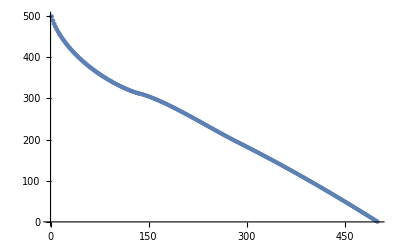

```mathematica
{val,vec}=Eigensystem[hamiltonian];
ListPlot[val]
```

0.283126

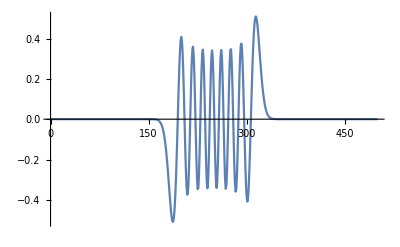

```mathematica
norm=Sqrt@Total[vec[[-1]]^2*dx]
ListPlot[vec[[-16]]/norm,PlotRange->All,Joined->True]
```

```mathematica
vec//Length
```

500

### 1D coherent state

```mathematica
Clear["Global`*"]
DSolve[y'[x]+m*ω/ℏ*x*y[x]-Sqrt[2*m*ω/ℏ]*α*(Cos[θ]+I*Sin[θ])*y[x]==0,y[x],x]//FullSimplify
DSolve[y'[x]+x*y[x]-Sqrt[2]*α*y[x]==0,y[x],x]//FullSimplify
```

{{y[x]→ⅇ^(√2 ⅇ^(ⅈ θ) x α √((m ω)/ℏ)-(m x^2 ω)/(2 ℏ)) C[1]}}

{{y[x]→ⅇ^(-x^2/2+√2 x α) C[1]}}

```mathematica
Clear["Global`*"]
Integrate[Exp[-x^2+Sqrt[2]*(α+αα)*x],{x,-Infinity,Infinity},Assumptions->m>0&&ω>0&&ℏ>0]
```

ⅇ^(1/2 (α+αα)^2) √π

```mathematica
Clear["Global`*"]
m=1.;
ω=2.;
ℏ=1.;
freal[x_,α_]:=(m*ω/Pi/ℏ)^(1/4)*Exp[-m*ω/2/ℏ*(x-Sqrt[2*ℏ/m/ω]*α)^2];
fimag[x_,α_]:=(m*ω/Pi/ℏ)^(1/4)*Exp[-m*ω/2/ℏ*x^2]*(Cos[α*Sqrt[2*m*ω/ℏ]*x]+I*Sin[α*Sqrt[2*m*ω/ℏ]*x]);
fcomplex[x_,real_,imag_]:=(m*ω/Pi/ℏ)^(1/4)*Exp[-m*ω/2/ℏ*(x-Sqrt[2*ℏ/m/ω]*real)^2]*(Cos[Sqrt[2*m*ω/ℏ]*imag*x]+I*Sin[Sqrt[2*m*ω/ℏ]*imag*x]);
```

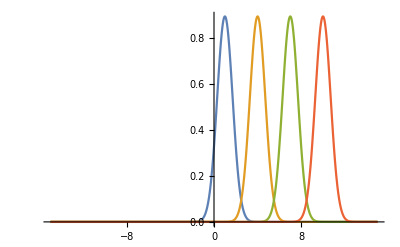

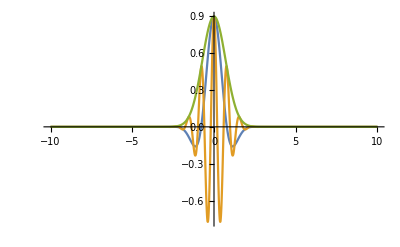

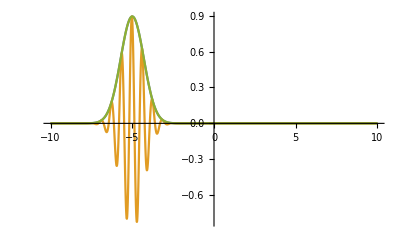

```mathematica
Plot[{freal[x,1],freal[x,4],freal[x,7],freal[x,10]},{x,-15,15},PlotRange->All]
Plot[{Re@fimag[x,1],Re@fimag[x,4],Abs@fimag[x,10]},{x,-10,10},PlotRange->All]
Plot[{freal[x,-5],Re@fcomplex[x,-5,5],Abs@fcomplex[x,-5,5]},{x,-10,10},PlotRange->All]
```

```mathematica
Clear["Global`*"]
m=1.;
ω=0.5;
ℏ=1.;
α0=5.1-.1*I;
real[t_]:=Re[α0]*Cos[ω*t]+Im[α0]*Sin[ω*t];
imag[t_]:=Im[α0]*Cos[ω*t]-Re[α0]*Sin[ω*t];
f[x_,t_]:=(m*ω/Pi/ℏ)^(1/4)*Exp[-m*ω/2/ℏ*(x-Sqrt[2*ℏ/m/ω]*real[t])^2]*(Cos[Sqrt[2*m*ω/ℏ]*imag[t]*x]+I*Sin[Sqrt[2*m*ω/ℏ]*imag[t]*x]);
```

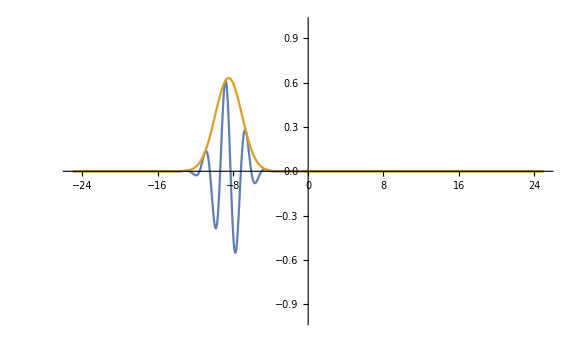

```mathematica
Monitor[
Do[
plot=Plot[{Re@f[x,t],Abs@f[x,t]},{x,-25,25},PlotRange->{{-25,25},{-1,1}},ImageSize->Large];
Pause[0.05];
,{t,0,20,0.05}];
,plot]
plot
```

### arbitrary superposition of eigenstates

```mathematica
Clear["Global`*"]
ℏ=1.;
ω=0.5;
m=1.;

α=Sqrt[m*ω/ℏ];
f[x_,n_]:=Sqrt[1/2^n/n!]*(m*ω/Pi/ℏ)^0.25*Exp[-α^2*x^2/2.]*HermiteH[n,α*x];
isOrthonormal[x_,n1_,n2_]:=Integrate[f[x,n1]*f[x,n2],{x,-Infinity,Infinity}];
```

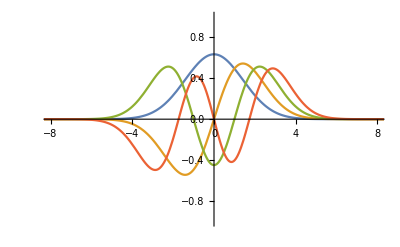

```mathematica
Plot[{f[x,0],f[x,1],f[x,2],f[x,3]},{x,-10,10},PlotRange->{{-8,8},{-1,1}}]
```

0.364665 ⅇ^(-0.25 x^2)+0.364665 ⅇ^(-0.25 x^2) x+0.128929 ⅇ^(-0.25 x^2) (-2.+2. x^2)

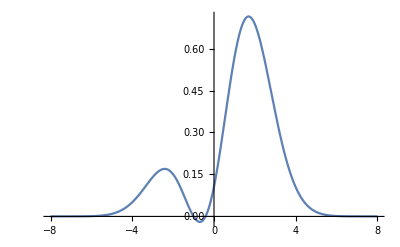

```mathematica
ff[x_]:=1/Sqrt[3.]*f[x,0]+1/Sqrt[3.]*f[x,1]+1/Sqrt[3.]*f[x,2];
ff[x]
Plot[ff[x],{x,-8,8},PlotRange->All]
```

```mathematica
fff[x_,t_]:=1/Sqrt[3.]*((Cos[ω/2.*t]*f[x,0]+Cos[3/2.*ω*t]*f[x,1]+Cos[5/2.*ω*t]*f[x,2])-I*(Sin[ω*t/2.]*f[x,0]+Sin[3/2.*ω*t]*f[x,1]+Sin[5/2.*ω]*f[x,2]));
```

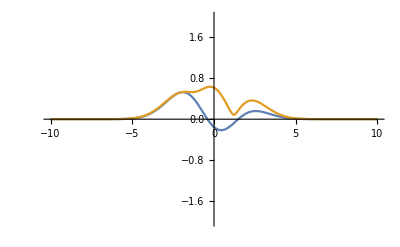

```mathematica
Monitor[
Do[
plot=Plot[{Re@fff[x,t],Abs@fff[x,t]},{x,-10,10},PlotRange->{All,{-2,2}}];
Pause[0.01];
,{t,0,20,0.1}];
,plot]
plot
```